Q1: Find the first three roots of the Bessel function J_1(x).

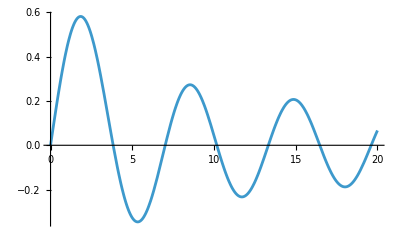

```mathematica
Plot[BesselJ[1,x],{x,0,20}]
```

```mathematica
FindRoot[BesselJ[1,x],{x,3.5}]
FindRoot[BesselJ[1,x],{x,7.0}]
FindRoot[BesselJ[1,x],{x,10.0}]
```

{x→3.83171}

{x→7.01559}

{x→10.1735}

Q2: Integrate the expression f(x) = sin(x) e^-x, and then take its derivative.

```mathematica
f=Sin[x] ⅇ^-x
```

ⅇ^-x Sin[x]

```mathematica
F=Integrate[f,x]
Df=D[F,x]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

-1/2 ⅇ^-x (Cos[x]-Sin[x])+1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
Simplify[Df]
```

ⅇ^-x Sin[x]

Q3 : Solve the equation  x ln (x) - 3 x + 10 = 6, both symbolically and numerically .

```mathematica
sol=Solve[x Log[x]-3 x+10==6,x,Reals]
```

{{x→ⅇ^(3+ProductLog[-4/ⅇ^3])},{x→ⅇ^(3+ProductLog[-1,-4/ⅇ^3])}}

```mathematica
N[sol,5]
```

{{x→15.523},{x→1.5688}}

```mathematica
ClearAll["Global`*"]
```